## Diffusion in Two Dimensions

## Completed and Analyzed in class, April 18, 2025

This is our twenty-first notebook. Now we are graduating to two-dimensional diffusion:

-Graphics-

### Two-Dimeinsional Diffusion — Theory

In one dimension, we had:

c(T,x) dT/dt=σ(x)(d^2 T)/(d x^2)

The obvious generalization to two dimensions is:

c(T,x,y) dT/dt=σ(x,y)((d^2 T)/(d x^2)+(d^2 T)/(d y^2))

Review the previous notebook if you need to be reminded how we specified the one-dimensional differential equation. We just have to add another dimension:

```mathematica
Module[{c=1, sigma=1},{ c Derivative[1,0,0][temp][t,x,y]==sigma (Derivative[0,2,0][temp][t,x,0]+Derivative[0,0,2][temp][t,0,y])}] // TraditionalForm
```

{temp^(1,0,0)(t,x,y)==temp^(0,2,0)(t,x,0)+temp^(0,0,2)(t,0,y)}

### HAVEN’T STARTED Adding the Boundary Conditions

Let’s give the rod a length and hold one end of it in the forge at some high temperature and the other end in an ice bath. Our boundary conditions are then:

```mathematica
length=1;
forgeTemp=1000;
iceBathTemp=0;

Module[{c=10, sigma=1/10 },{ c Derivative[1,0][temp][t,x]==sigma Derivative[0,2][temp][t,x],temp[t,0]==forgeTemp,temp[t,length]==iceBathTemp}] // TraditionalForm
```

{10 temp^(1,0)(t,x)==1/10 temp^(0,2)(t,x),temp(t,0)==1000,temp(t,1)==0}

### Adding the Initial Conditions

The rod might be quite non-uniformly heated at t=0. The interesting thing is then, how will the heat diffuse along the rod. Let’s try a jagged initial function:

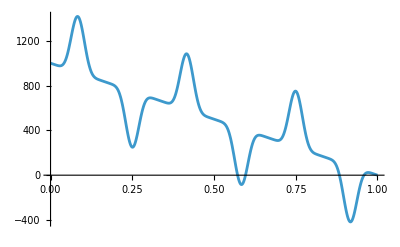

```mathematica
numberOfJaggies=6;
amplitudeOfJaggies=500;
lengthOfJaggies=length/numberOfJaggies;
f[x_]:=amplitudeOfJaggies Sin[(Pi x)/lengthOfJaggies]^7+forgeTemp+ (iceBathTemp-forgeTemp)x/length

Plot[f[x],{x,0,length}]
```

```mathematica
oneDimensionalDiffusionProblem=Module[{c=10, sigma=1/10 },{ c Derivative[1,0][temp][t,x]==sigma Derivative[0,2][temp][t,x],temp[t,0]==forgeTemp,temp[t,length]==iceBathTemp,temp[0,x]==f[x]}]
```

{10 temp^(1,0)[t,x]==1/10 temp^(0,2)[t,x],temp[t,0]==1000,temp[t,1]==0,temp[0,x]==1000-1000 x+500 Sin[6 π x]^7}

### Making Mathematica Numerically Solve the Problem

```mathematica
oneDimensionalDiffusionSolutionRule = NDSolve[oneDimensionalDiffusionProblem,temp,{t,0,10},{x,0,length}][[1]]
```

{temp→InterpolatingFunction[{{0., 10.}, {0., 1.}}, <>]}

Convert the rule to a function:

```mathematica
oneDimensionalDiffusionSolution[t_,x_]=temp[t,x]/.oneDimensionalDiffusionSolutionRule
```

InterpolatingFunction[{{0., 10.}, {0., 1.}}, <>][t,x]

### Plotting the Numerical Solution at t=1/10

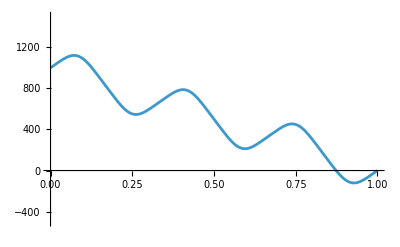

```mathematica
Plot[oneDimensionalDiffusionSolution[1/10,x],{x,0,length},PlotRange->{{0,length},{-amplitudeOfJaggies,forgeTemp+amplitudeOfJaggies}}]
```

### Animating the Numerical Solution

```mathematica
Animate[Plot[oneDimensionalDiffusionSolution[t,x],{x,0,length},PlotRange->{{0,length},{-amplitudeOfJaggies,forgeTemp+amplitudeOfJaggies}}],{t,0,1},DefaultDuration->10,AnimationRunning->False]
```

The fact that this isn’t some simple sine wave is part of what gives the guitar its tone or timber. You can exaggerate this effect by picking the string very near the bridge.